## Random walker

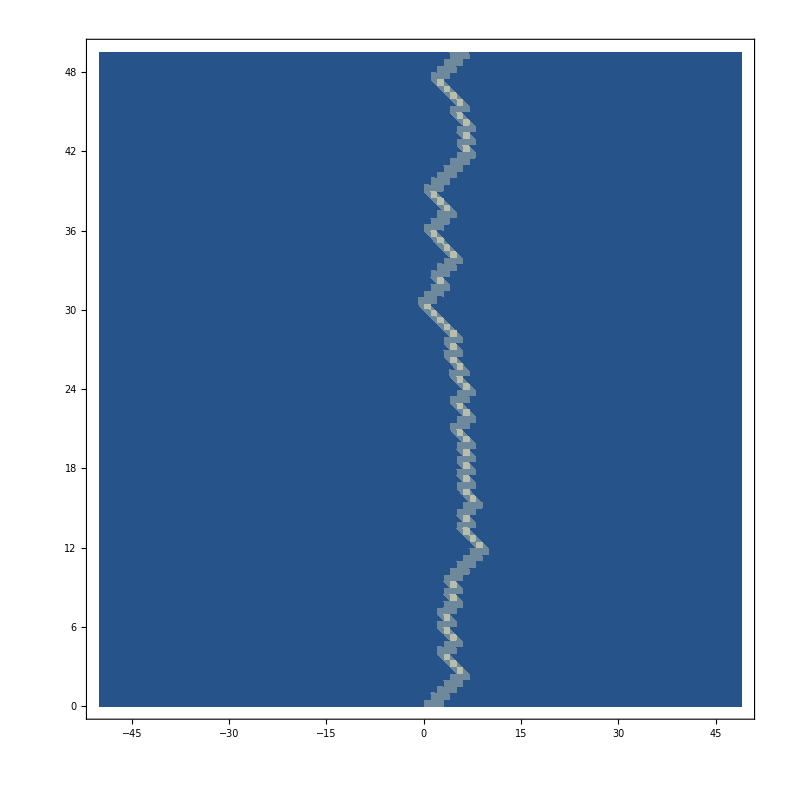

```mathematica
A=Import["~/Programs/RandomWalk/Data/Sz.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<3&)];
(*A=Cases[A,_?(#[[2]]≠0&)](*if σ doesn't change -> dont print it*);*)
A=A[[;;,{1,3,2}]](*x,t,σ*);
ListDensityPlot[A]
```

## Some results on exponent

-Graphics-

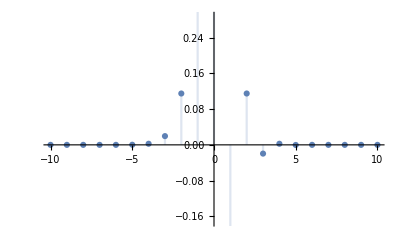

```mathematica
DiscretePlot[{BesselJ[n,-1],{n,-10,10}]
```

```mathematica
BesselJ[-2,x]//Simplify
```

BesselJ[2,x]